## Lesson

Get output of last computation:

```mathematica
3
```

3

```mathematica
%
```

3

Assign value to variable:

```mathematica
x=3
```

3

```mathematica
x
```

3

Remove value from variable:

```mathematica
Clear[x]
```

```mathematica
x
```

x

Set up a local variable:

```mathematica
Module[{a=3},2a]
```

6

```mathematica
a
```

a

Compute a value but suppress output:

```mathematica
y=3;
```

Do a sequence of computations:

```mathematica
a=1;b=2;
```

## Questions

Q1. Use Module to compute x^2+x where x is Range[10].

```mathematica
Module[{x=Range[10]},x^2+x]
```

{2,6,12,20,30,42,56,72,90,110}

Q2. Use Module to generate a list of 10 random integers up to 100, then make a column giving the original list, and the results of applying Sort, Max and Total to it.

```mathematica
Module[{x=RandomInteger[100,10]},Column[{x,Sort[x],Max[x],Total[x]}]]
```

{60,53,11,88,75,15,82,7,41,81}
{7,11,15,41,53,60,75,81,82,88}
88
513

Q3. Use Module to generate an image collage from a picture of a giraffe, and the results of applying Blur, EdgeDetect and ColorNegate to it.

```mathematica
Module[{x=Entity["TaxonomicSpecies","GiraffaCamelopardalis::y5488"]["Image"]},ImageCollage[{x,Blur[x],EdgeDetect[x],ColorNegate[x]}]]
```

-Graphics-

Q4. Inside a Module, let r=Range[10], then make a line plot of r joined with the reverse of r joined with r joined with the reverse of r.

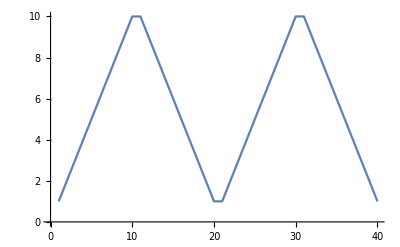

```mathematica
Module[{r=Range[10]},ListLinePlot[Join[r,Reverse[r],r,Reverse[r]]]]
```

Q5. Find a simpler form for {Range[10]+1, Range[10]-1, Reverse[Range[10]]}.

```mathematica
{Range[10]+1,Range[10]-1,Reverse[Range[10]]}
```

```mathematica
Module[{x=Range[10]},{x+1,x-1,Reverse[x]}]
```

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

Q6. Find a simpler form for Module[{u=10}, Join[{u}, Table[u=Mod[17u+2, 11], 20]]].

```mathematica
NestList[Mod[17#+2,11]&,10,20]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

Q7. Generate 10 random strings made of 5 letters, in which consonants (non-vowels) alternate with vowels (aeiou).

```mathematica
Table[StringJoin[Module[{v=Characters["aeiou"],c},c=Complement[Alphabet[],v];
RandomChoice/@{c,v,c,v,c}]],10]
```

{zuqen,dulot,maqaq,pazef,wakac,raciz,koxab,duhal,natur,mapej}